# Reaction-Diffusion CRNs

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

## Well-mixed CRN simulator preliminaries

First verify that I can run well-mixed CRN simulations.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
```

```mathematica
predprey={
rxn[F,0,1],
rxn[R,2R,1],
rxn[R+F,2F,1.5],
conc[R,2],
conc[F,1]
}
```

{  F⟶^10,  R⟶^12 R,  F+R⟶^1.52 F,conc[R,2],conc[F,1]}

```mathematica
SpeciesInRxnsys[predprey]
```

{F,R}

```mathematica
RxnsysToOdesys[predprey] // MatrixForm
```

(F'[t]==-F[t]+1.5 F[t] R[t]
R'[t]==R[t]-1.5 F[t] R[t]
R[0]==2
F[0]==1)

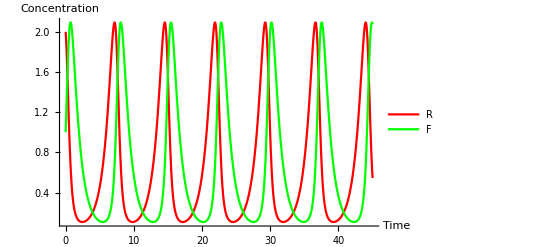

```mathematica
tmax=45;sol=SimulateRxnsys[predprey,tmax];Plot[Evaluate[{R[t],F[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},AxesLabel->{Time,Concentration},PlotLegends->{R,F}]
```

```mathematica
bistable={
rxn[2A+B,3A,1],
rxn[A+2B,3B,1],
conc[A,0.6],conc[B,0.4]
}
```

{  2 A+B⟶^13 A,  A+2 B⟶^13 B,conc[A,0.6],conc[B,0.4]}

```mathematica
SpeciesInRxnsys[bistable]
```

{A,B}

```mathematica
RxnsysToOdesys[ bistable] // MatrixForm
```

(A'[t]==A[t]^2 B[t]-A[t] B[t]^2
B'[t]==-A[t]^2 B[t]+A[t] B[t]^2
A[0]==0.6
B[0]==0.4)

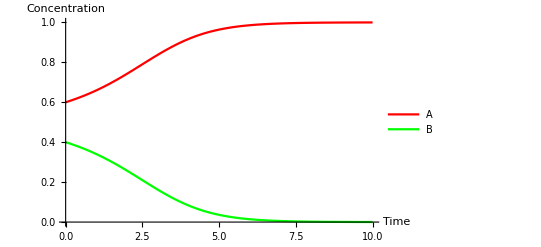

```mathematica
tmax=10;sol=SimulateRxnsys[bistable,tmax];Plot[Evaluate[{A[t],B[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{{Red},{Green}},AxesLabel->{Time,Concentration},PlotLegends->{A,B}]
```

## Hand-coding reaction-diffusion simulation with Euler integration

Now hand-code reaction-diffusion with discrete Laplacian and Euler integration on a torus.

```mathematica
BistableRDstep[{spaceA_,spaceB_},{DA_,DB_},dx_,dt_,steps_]:=Module[{A=spaceA,B=spaceB,diffA,diffB,ker={{1,2,1},{2,-12,2},{1,2,1}}/12.0},
Do[
diffA=DA*ListConvolve[ker,A,2]*dt/dx^2+(A*A*B-A*B*B)*dt;
diffB=DB*ListConvolve[ker,B,2]*dt/dx^2+(-A*A*B+A*B*B)*dt;
A+=diffA; B+=diffB,
steps];
{A,B}
]
```

```mathematica
SA=Table[RandomReal[],100,100]*.5;
SB=Table[RandomReal[],100,100]*.5;
time=0;
```

```mathematica
Dynamic[{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}]
```

```mathematica
With[{dt=0.01,its=10},Do[
{SA,SB}=BistableRDstep[{SA,SB},{1,1},1,dt,its]; time+=dt*its,
1000]];
```

Now let’s look for more interesting pattern formation using the Gray-Scott reactions.  

Thanks to parameters and initial conditions borrowed from Rajesh Singh’s blog:    https://rajeshrinet.github.io/blog/2016/gray-scott/       But probably due to my 9-point 3x3 kernel versus his 5-point kernel,  some initial condition adjustments had to be made.  In fact, I found it challenging to set up good initial conditions, and the hack I used below is certainly more complicated than it needs to be.
    
A nice academic reference is Pearson, “Complex patterns in a simple system”: https://doi.org/10.1126/science.261.5118.189    
    
I forget where, but somewhere I saw a beautiful way to illustrate how the pattern formation depends on the parameters:  perform a simulation on a large spatial area where the parameters depend upon the spatial position.  So in different positions, you’ll get a different type of pattern -- and they’ll seamlessly blend into each other.  We’ll start out by doing that, and then look back to where we see certain types of patterns so as to read off the parameters that ought to generate the desired kind of pattern (from the “right” initial conditions, at least).

```mathematica
Clear[GrayScottRDstep]
GrayScottRDstep[{spaceA_,spaceB_},{DA_,DB_,f_,k_},dx_,dt_,steps_]:=Module[{A=spaceA,B=spaceB,diffA,diffB,ker={{1,2,1},{2,-12,2},{1,2,1}}/12.0},
Do[
diffA=DA*ListConvolve[ker,A,2]*dt/dx^2+(f*(1-A)-A*B*B)*dt;
diffB=DB*ListConvolve[ker,B,2]*dt/dx^2+(-(f+k) B+A*B*B)*dt;
A+=diffA; B+=diffB,
steps];
{A,B}
]
```

```mathematica
Clear[InitGrayScott]
InitGrayScott[N_,r_,noise_:0.2]:=With[{N2=Round[N/2]},
SA=Table[RandomReal[]*noise,N,N];
SB=Table[RandomReal[]*noise,N,N];
SA[[N2-r;;N2+r,N2-r;;N2+r]]=0.5;
SB[[N2-r;;N2+r,N2-r;;N2+r]]=0.25;
time=0;
]
```

Here is the reaction-diffusion “phase diagram” image... nice and big (and very slow).  Note that we didn’t have to change any code -- just rather than being a scalar constant, the parameters k and f are now arrays of the same size as the reaction-diffusion space.  This works because Mathematica defaults to element-wise multiplication and addition for matrices.

f varies vertically; k varies horizontally.

Remember to delete Dynamic output (e.g. above) before going on to the next section -- I am re-using variable names SA and SB all over the place...

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}]
```

```mathematica
With[{N=500},With[{dt=0.25,its=20,
k=Table[0.05+0.02j/N,{i,N},{j,N}],
f=Table[0.02+0.04 i/N,{i,N},{j,N}]},
InitGrayScott[N,1,0.8];
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.16,0.08,f,k},0.5,dt,its]; time+=dt*its,
20000]]]
```

```mathematica
{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}
```

{-Graphics-,-Graphics-,100000.,185989.,{1.,0.219419},{0.452176,9.87951×10^-18}}

```mathematica
ArrayPlot[MapThread[RGBColor,{SA,2 SB,Table[0.5,500,500]},2]]
```

-Graphics-

It seems that the pattern more or less stabilizes by t=100,000.   A faster movie would be fun because the dots move around and blink in and out as it tries to stabilize.

Try to dynamically watch a small version.  Also, this will build initial conditions that work well for other uniform parameter cases further below.

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time}]
```

```mathematica
With[{N=150},With[{dt=0.25,its=20,
k=Table[0.05+0.02j/N,{i,N},{j,N}],
f=Table[0.02+0.04 i/N,{i,N},{j,N}]},
InitGrayScott[N,1,0.8];
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.16,0.08,f,k},0.5,dt,its]; time+=dt*its,
2000]]]
```

```mathematica
SAphase150=SA;SBphase150=SB;
```

“Bacteria” per Rajesh Singh: had to use end state of phase image (above) as initial conditions -- otherwise, died out too easily.

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time}]
```

```mathematica
With[{dt=0.25,its=20},(*InitGrayScott[150,10,0.2];*) {SA,SB}={SAphase150,SBphase150};time=0;
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.14,0.06,0.035,0.065},0.5,dt,its]; time+=dt*its,
1000]]
```

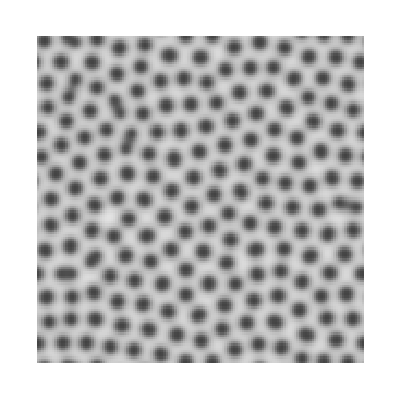
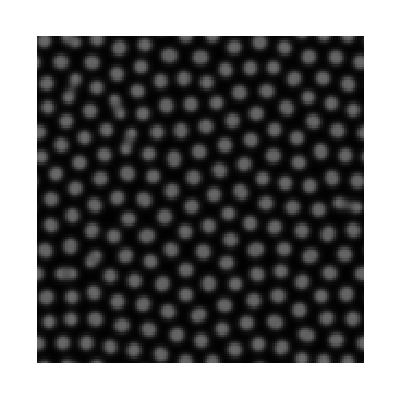
{-Graphics-,-Graphics-,5000.,17115.9,{0.887992,0.260758},{0.416655,0.00220133}}

```mathematica
{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}
```

“Coral Patterns” per Rajesh Singh.

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time}]
```

```mathematica
With[{dt=0.25,its=20},InitGrayScott[150,10];
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.16,0.08,0.06,0.062},0.5,dt,its]; time+=dt*its,
4000]]
```

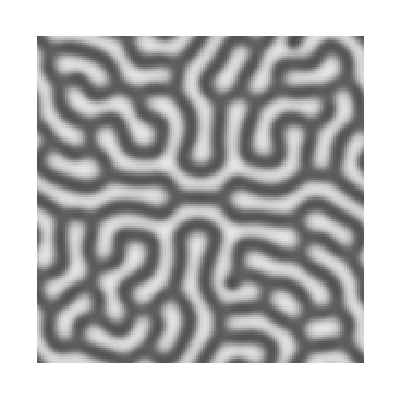
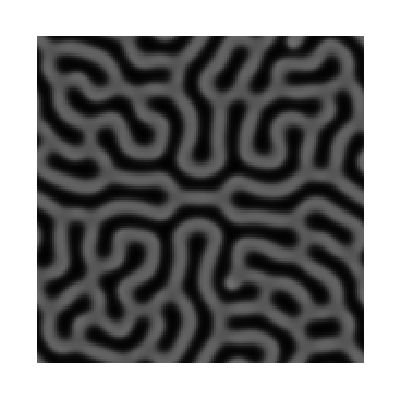
{-Graphics-,-Graphics-,20000.,17588.2,{0.897823,0.305611},{0.430039,0.00772694}}

```mathematica
{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}
```

“Spirals” was originally {0.12,0.08,0.02,0.05} -- changed diffusion and initial conditions.  The “spirally” behavior doesn’t really jump out at me.

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time}]
```

```mathematica
With[{dt=0.25,its=20},(*InitGrayScott[150,40,0.05];*) {SA,SB}={SAphase150,SBphase150};time=0;
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.08,0.04,0.02,0.05},0.5,dt,its]; time+=dt*its,
4000]]
```

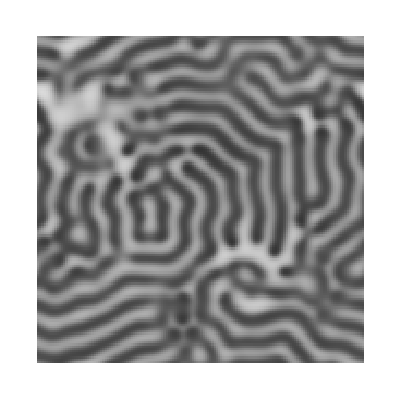
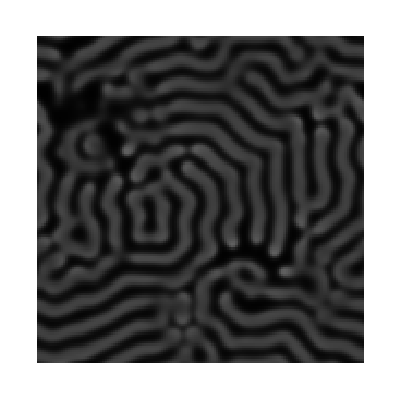
{-Graphics-,-Graphics-,20000.,13817.2,{0.853001,0.202488},{0.37606,0.00232668}}

```mathematica
{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}
```

“Zebrafish” per per Rajesh Singh.

```mathematica
Dynamic[{ArrayPlot[SA],ArrayPlot[SB],time}]
```

```mathematica
With[{dt=0.25,its=20},(*InitGrayScott[150,40,0.05];*) {SA,SB}={SAphase150,SBphase150};time=0;
Do[
{SA,SB}=GrayScottRDstep[{SA,SB},{0.16,0.08,0.035,0.06},0.5,dt,its]; time+=dt*its,
4000]]
```

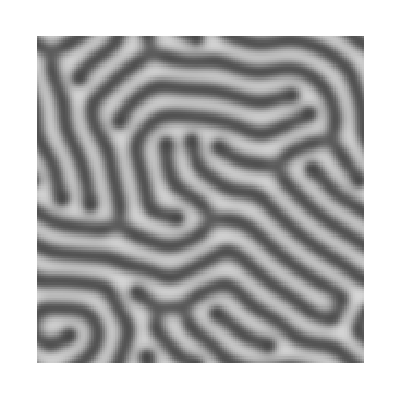
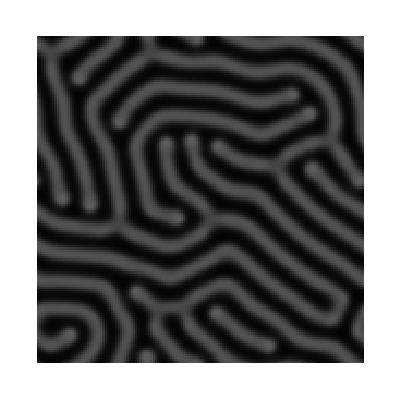
{-Graphics-,-Graphics-,20000.,16052.9,{0.834865,0.283154},{0.367958,0.00997438}}

```mathematica
{ArrayPlot[SA,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],ArrayPlot[SB,ColorFunctionScaling->False,ColorRules->{v_:>GrayLevel[Max[0,Min[1,v]]]}],time,Total[Flatten[Join[SA,SB]]],{Max[Flatten[SA]],Min[Flatten[SA]]},{Max[Flatten[SB]],Min[Flatten[SB]]}}
```

## Automating the conversion of well-mixed CRNs to the reaction-diffusion context

We would like to automate the compilation of an arbitrary CRN (in Soloveichik’s format) to an RD system.   One option would be to symbolically build up code like the above, but first computing the flux for each reaction (in each spatial cell) and then computing the diffusion and the species concentration changes -- then compile that symbolic code to C.  Another option would be to avoid compilation entirely and find a way to express general-purpose RD simulation in terms of already-fast numerical primitives.  That’s what we’ll do.  Remarkably, it’s just a few lines of code (on top of Soloveichik’s simulator).

```mathematica
CRNSimulatorRD[crn_,Ds_]:=With[{
species=SpeciesInRxnsys[crn],
numspecies=Length[SpeciesInRxnsys[crn]],
eqns=(First[Cases[RxnsysToOdesys[crn],Equal[Derivative[1][#][t],flux_]:>flux]]/.x_Symbol[t]:>x)& /@SpeciesInRxnsys[crn],
ker={{1,2,1},{2,-12,2},{1,2,1}}/12.0
},
With[{reactForm=Table[eqns[[i]]/.Table[species[[j]]->"S"[j],{j,numspecies}],{i,numspecies}]},
Function[{S0,dx,dt,steps},
Module[{S=S0,diff,react},Do[
diff=Table[(species[[i]]/.Ds) * ListConvolve[ker,S[[i]],2],{i,numspecies}];
react=reactForm/.{"S"[i_]:>S[[i]]};
S+=diff*dt/dx^2+react*dt,
steps];
S
]]]]
```

Given a CRN, we generate a function that simulates RD from a given state, for a certain number of steps.  We show that it agrees with the hand-coded version.  And is about as fast.  (Note that the diffusion constants are given by the second argument, which is a list of replacement rules.)  Doesn’t look pretty, but seems to work.

```mathematica
bistable
```

{  2 A+B⟶^13 A,  A+2 B⟶^13 B,conc[A,0.6],conc[B,0.4]}

```mathematica
bistableRD=CRNSimulatorRD[bistable,{A->1,B->1}]
```

Function[{S0$,dx$,dt$,steps$},Module[{S$=S0$,diff$,react$},Do[diff$=Table[({A,B}⟦i⟧/.{A→1,B→1}) ListConvolve[{{0.0833333,0.166667,0.0833333},{0.166667,-1.,0.166667},{0.0833333,0.166667,0.0833333}},S$⟦i⟧,2],{i,2}];react$={S[1]^2 S[2]-S[1] S[2]^2,-S[1]^2 S[2]+S[1] S[2]^2}/.{S[i$_]:>S$⟦i$⟧};S$+=(diff$ dt$)/dx$^2+react$ dt$,steps$];S$]]

```mathematica
SA=Table[RandomReal[],100,100]*.5;
SB=Table[RandomReal[],100,100]*.5;
time=0;
```

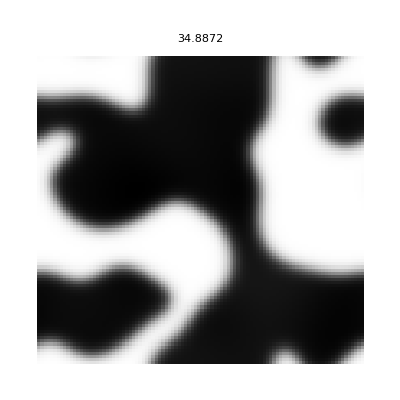
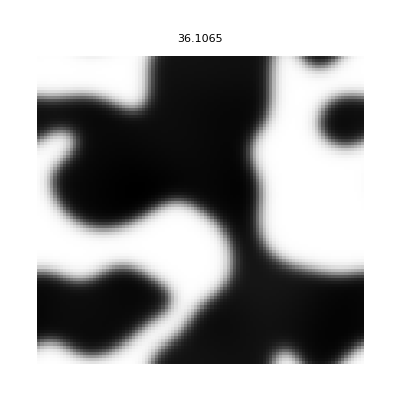

```mathematica
With[{tmax=10000,dx=1,dt=0.01},ArrayPlot[First[Last[#]],PlotLabel->First[#]]&/@
{Timing[BistableRDstep[{SA,SB},{1,1},dx,dt,tmax]],Timing[bistableRD[{SA,SB},dx,dt,tmax]]} ]
```

It also works for the Gray-Scott system.  Here, we explicitly back out what the CRN for the Gray-Scott system actually is, since normally papers just present the partial differential equations.

```mathematica
grayscottRD=CRNSimulatorRD[{rxn[A+2B,3B,1],rxn[B,0,f+k],rxn[0,A,f],rxn[A,0,f]}/.{f->0.06,k->0.062},{A->0.16,B->0.08}]
```

Function[{S0$,dx$,dt$,steps$},Module[{S$=S0$,diff$,react$},Do[diff$=Table[({A,B}⟦i⟧/.{A→0.16,B→0.08}) ListConvolve[{{0.0833333,0.166667,0.0833333},{0.166667,-1.,0.166667},{0.0833333,0.166667,0.0833333}},S$⟦i⟧,2],{i,2}];react$={0.06-0.06 S[1]-S[1] S[2]^2,-0.122 S[2]+S[1] S[2]^2}/.{S[i$_]:>S$⟦i$⟧};S$+=(diff$ dt$)/dx$^2+react$ dt$,steps$];S$]]

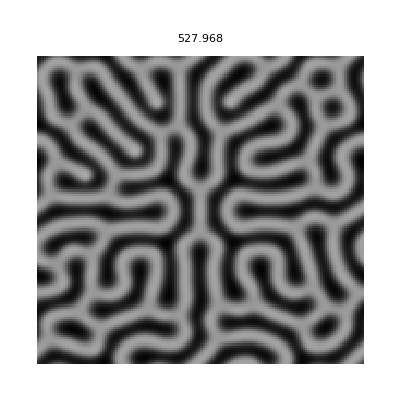
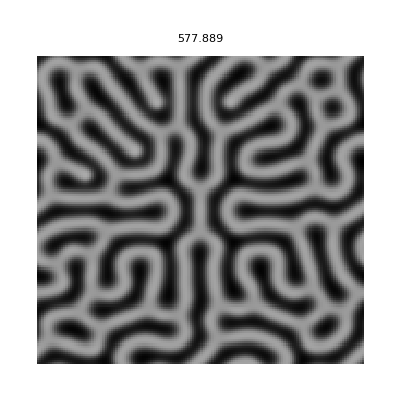

```mathematica
With[{tmax=80000,dx=0.5,dt=0.25},
InitGrayScott[150,10];
ArrayPlot[First[Last[#]],PlotLabel->First[#]]&/@
{Timing[GrayScottRDstep[{SA,SB},{0.16,0.08,0.06,0.062},dx,dt,tmax]],Timing[grayscottRD[{SA,SB},dx,dt,tmax]]} ]
```

```mathematica
Dynamic[ArrayPlot[SA]]
```

```mathematica
InitGrayScott[150,10];Do[{SA,SB}=grayscottRD[{SA,SB},0.5,1,20],4000]; (* fast: about as large as dt can get, here *)
```

I declare this a success!  It is a tad slower than a hand-coded version, which is in principle unnecessary, but the margin is just usually less than 15%, so it’s quite tolerable.   Actually computing each reaction’s flux separately and then adding/subtracting for each affected species would also speed things up by a factor of about 3 to 4 for typical CRNs, I would think.   But this code was simpler...

What does the predator-prey system do?  Well, it depends on initial conditions (and one could explore reaction rate parameters and diffusion constants as well).

```mathematica
RxnsysToOdesys[predprey]
```

{F'[t]==-F[t]+1.5 F[t] R[t],R'[t]==R[t]-1.5 F[t] R[t],R[0]==2,F[0]==1}

```mathematica
predpreyRD=CRNSimulatorRD[DeleteCases[predprey,_conc],{F->0.1,R->0.1}]
```

Function[{S0$,dx$,dt$,steps$},Module[{S$=S0$,diff$,react$},Do[diff$=Table[({F,R}⟦i⟧/.{F→0.1,R→0.1}) ListConvolve[{{0.0833333,0.166667,0.0833333},{0.166667,-1.,0.166667},{0.0833333,0.166667,0.0833333}},S$⟦i⟧,2],{i,2}];react$={-S[1]+1.5 S[1] S[2],S[2]-1.5 S[1] S[2]}/.{S[i$_]:>S$⟦i$⟧};S$+=(diff$ dt$)/dx$^2+react$ dt$,steps$];S$]]

```mathematica
With[{N=200},SF=Table[If[0.45N <i<0.5N && .2N<j<.8N,0.8,0],{i,N},{j,N}];SR=Table[If[0.5N <i<0.55N && .2N<j<.8N,0.8,0],{i,N},{j,N}];]
```

```mathematica
With[{N=200},SF=Table[If[i>N/2,0.1,0.5],{i,N},{j,N}];SR=Table[If[j>N/2,0.1,0.5],{i,N},{j,N}];]
```

```mathematica
With[{N=200},SF=Table[RandomReal[],{i,N},{j,N}];SR=Table[RandomReal[],{i,N},{j,N}];]
```

```mathematica
Dynamic[{ArrayPlot[SF],ArrayPlot[SR],{time,Max[Flatten[SF]],Max[Flatten[SR]]}}]
```

```mathematica
time=0;With[{dt=0.01,its=1},Do[{SF,SR}=predpreyRD[{SF,SR},0.2,dt,its];time+=dt its,40000]];
```

How about a nice excitable media RD system, such as the Oregonator, where we can watch beautiful spiral waves form?  Don’t bother here...  parameters not sorted out yet...

```mathematica
Oregonator={ rxn[Y,X,8],rxn[X+Y,0,10],rxn[X,2X+2Z,1],rxn[2X,0,0.5],rxn[Z,Y,0.5] }
```

{  Y⟶^8X,  X+Y⟶^100,  X⟶^12 X+2 Z,  2 X⟶^0.50,  Z⟶^0.5Y}

```mathematica
OregonRD=CRNSimulatorRD[Oregonator,{X->1,Y->1,Z->0.6}]
```

Function[{S0$,dx$,dt$,steps$},Module[{S$=S0$,diff$,react$},Do[diff$=Table[({X,Y,Z}⟦i⟧/.{X→1,Y→1,Z→0.6}) ListConvolve[{{0.0833333,0.166667,0.0833333},{0.166667,-1.,0.166667},{0.0833333,0.166667,0.0833333}},S$⟦i⟧,2],{i,3}];react$={S[1]-1. S[1]^2+8 S[2]-10 S[1] S[2],-8 S[2]-10 S[1] S[2]+0.5 S[3],2 S[1]-0.5 S[3]}/.{S[i$_]:>S$⟦i$⟧};S$+=(diff$ dt$)/dx$^2+react$ dt$,steps$];S$]]

```mathematica
With[{N=200},SX=Table[If[i>N/2,0.1,0.5],{i,N},{j,N}];SY=Table[If[j>N/2,0.1,0.5],{i,N},{j,N}];SZ=Table[0.5,N,N]];
```

```mathematica
With[{N=200},SX=Table[RandomReal[],{i,N},{j,N}];SY=Table[RandomReal[],{i,N},{j,N}];SZ=Table[RandomReal[],N,N]];
```

```mathematica
Dynamic[{ArrayPlot[Transpose[{SX,SY,SZ},{3,1,2}]/Max[Flatten[{SX,SY,SZ}]]],Max[Flatten[{SX,SY,SZ}]],time}]
```

```mathematica
time=0;With[{dt=0.001,its=1},Do[{SX,SY,SZ}=OregonRD[{SX,SY,SZ},0.2,dt,its];time+=dt its,4000]];
```

$Aborted

And you want to program reaction-diffusion systems to do something interesting, like construct a pre-prefined image or simulate a cellular automaton?  It can be done... in theory, and to some extent in practice...

Spatial waves in synthetic biochemical networks - A Padirac, T Fujii, A Estévez-Torres, Y Rondelez - Journal of the American Chemical Society, 2013
Designing modular reaction-diffusion programs for complex pattern formation - D Scalise, R Schulman - Technology, 2014
Emulating cellular automata in chemical reaction–diffusion networks - D Scalise, R Schulman - Natural Computing, 2016
Pattern generation with nucleic acid chemical reaction networks - SS Wang, AD Ellington - Chemical Reviews, 2019 
Differentiable Programming of Reaction-Diffusion Patterns - A Mordvintsev, E Randazzo, E Niklasson - arXiv preprint arXiv:2107.06862, 2021